```mathematica
dataOverall1=Import[NotebookDirectory[]<>"/overall_post.csv","CSV"] ;(*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

```mathematica
dataOverall2=Import[NotebookDirectory[]<>"/-1pn-all-beta.csv","CSV"] ; (*PPE beta*)
dataOverall3=Import[NotebookDirectory[]<>"/-1pn-all-alpha.csv","CSV"] ;(*PPE alpha*)
```

```mathematica
χ1All=dataOverall1[[All,7]]; (*Dimensionles spin parameter*)
χ2All=dataOverall1[[All,8]];
```

```mathematica
m1All=dataOverall1[[All,5]]*tsolar/.tsolar->4.925491*10^-6;
m2All=dataOverall1[[All,6]]*tsolar/.tsolar->4.925491*10^-6;
```

```mathematica
ηAll=(m1All*m2All)/(m1All+m2All)^2;
```

```mathematica
βppEAll=1/1.64485*dataOverall2[[All,1]];(*1-sigma upper bound*)
αppEAll=1/1.64485*dataOverall3[[All,1]](*1-sigma upper bound*);
```

```mathematica
s1All=2/χ1All^2*(√(1-χ1All^2)-1+χ1All^2);
s2All=2/χ2All^2*(√(1-χ2All^2)-1+χ2All^2);
```

```mathematica
ζphaseAll=Abs[-7168/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*βppEAll] ;(*Sigma_Zeta from phase corrections.Eqn. 29 of 1809.00259*);
```

```mathematica
ζampAll=Abs[-192/5*((m1All+m2All)^4*ηAll^(18/5))/(((m1All^2*s2All)-(m2All^2*s1All))^2)*αppEAll]; (*Sigma_Zeta from amplitude corrections*)
```

```mathematica
Length[m1All]
```

52252

```mathematica
Length[βppEAll]
```

52252

```mathematica
Mean[ζampAll]
```

12509.6

```mathematica
Mean[ζphaseAll]
```

360.999

```mathematica
ζAllphaseSelected=Select[ζphaseAll,# <1 &]; (*Datasets that satisfy Zeta<1 where Zeta is found from phase correction. Since the distribution of zeta is Gaussian with zero mean, sigma_zeta<1 and zeta<1 are analogous*)
ζAllampSelected=Select[ζampAll,# <1 &];(*Datasets that satisfy Zeta<1 where Zeta is found from amplitude correction*)
```

```mathematica
Length[ζAllphaseSelected]
```

51355

```mathematica
Length[ζAllampSelected]
```

46872

```mathematica
Mean[ζAllphaseSelected]
```

0.0174016

```mathematica
StandardDeviation[ζAllphaseSelected]
```

0.074786

```mathematica
A1=Table[Append[dataOverall1[[i]],ζphaseAll[[i]]],{i,1,Length[dataOverall1]}]
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219},52250,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816,0.00193851}}
 |  |  |  |

```mathematica
A2=Table[Append[A1[[i]],ζampAll[[i]]],{i,1,Length[A1]}] (*Contains all the posterior data and sigma_zeta from both phase and amplitude corrections*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},52250,{0.795965,311.364,3.41712,6,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A3=Select[A2,#[[11]]<1&][[All,{1,2,3,4,5,6,7,8,9,10}]] (*Data satisfying zeta_phase<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195},51353,{0.795965,311.364,3.41712,-0.0397626,13.4479,9.18584,0.303922,0.287212,0.401218,0.583816}}
 |  |  |  |

```mathematica
A4=Select[A2,#[[12]]<1&][[All,{1,2,3,4,5,6,7,8,9,10,11,12}]](*Data satisfying zeta_amp<1*)
```

{{0.273997,245.073,3.58022,-0.392013,15.7931,8.16902,0.474815,0.0924668,0.861707,-0.349195,0.000527219,0.0171763},46870,{0.795965,311.364,3.41712,6,0.583816,0.00193851,0.0686092}}
 |  |  |  |

```mathematica
A4[[All,12]]
```

{0.0171763,0.0522075,0.165549,0.0378357,0.0127864,0.0533918,0.0167203,46858,0.0140803,0.0231292,0.000514475,0.0374042,0.727602,0.0315771,0.0686092}
 |  |  |  |

```mathematica
Length[A3]
```

51355

```mathematica
Length[A4]
```

46872

```mathematica
Select[A4[[All,11]],#>1&]  (*Proves that all 46872 data with zeta_amp<1 also satisfies zeta_phase<1*)
```

{}

```mathematica
Mean[ζAllampSelected]
```

0.094265

```mathematica
SqrtαEDGBamp=((ζampAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB (in km) from the amplitdue corrections of all data*)
SqrtαEDGBphase=((ζphaseAll*(m1All+m2All)^4)/(16*π))^(1/4)*3*10^5(*square root of alpha_EDGB from the phase corrections of all data*)
```

{4.81405,13.8985,6.13673,8.01727,12.5915,5.6388,4.50492,52238,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

{2.015,5.74447,2.52291,3.29495,5.19042,2.31966,1.90965,2.94321,52237,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
Mean[SqrtαEDGBamp] (*just a rough estimate for sanity check. This does not give a statistically meaningful bound*)
```

7.87527

```mathematica
Mean[SqrtαEDGBphase]
```

3.31329

```mathematica
tsolar=4.925491*10^-6
```

4.92549×10^-6

```mathematica
SqrtαEDGBphaseSelected=((A4[[All,11]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha_EDGB from phase correction of the data satisfying zeta_phase<1*)
```

{2.015,2.52291,3.29495,2.31966,1.90965,2.94321,2.04561,1.98368,46857,2.37185,2.2705,1.32689,2.36852,4.71202,2.23658,2.63558}
 |  |  |  |

```mathematica
SqrtαEDGBampSelected=((A4[[All,12]]*(A4[[All,5]]*tsolar+A4[[All,6]]*tsolar)^4)/(16*π))^(1/4)*3*10^5 (*square root of alpha from amplitude correction of the data satisfying zeta_amp<1*)
```

{4.81405,6.13673,8.01727,5.6388,4.50492,6.70477,4.82258,4.70667,46856,4.92185,5.14987,5.2601,2.76716,5.66867,11.4363,5.42432,6.42844}
 |  |  |  |

# compare two methods of integration

```mathematica
fun1=1/(√(2*π*(ζphaseAll)^2))*Exp[-x^2/(2Exp[2 Log[ζphaseAll]])] (*x is \[Zeta. and ζphaseAll is sigma_zeta from Fisher analysis*)
```

{756.691 ⅇ^(-1.79882×10^6 x^2),8.61832 ⅇ^(-233.343 x^2),267.496 ⅇ^(-224795. x^2),52247,437.105 ⅇ^(-600234. x^2),205.799 ⅇ^(-133056. x^2)}
 |  |  |  |

```mathematica
𝒟log=HistogramDistribution[Log[ζphaseAll]]
```

DataDistribution[…]

```mathematica
Histogram[Log[ζphaseAll]];
```

```mathematica
Histogram[ζphaseAll];
```

```mathematica
ps1=PDF[𝒟log,x];
```

```mathematica
ps2[x]=ps1;
```

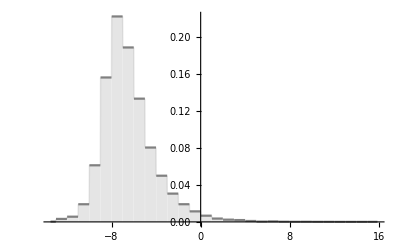

```mathematica
plottest2=Plot[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]},Filling->Axis,PlotStyle->Gray,PlotRange->All]
```

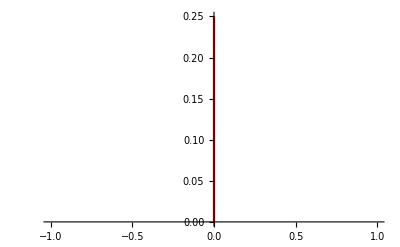

```mathematica
zeta1=ListLinePlot[{{0,0},{0,0.25}},PlotStyle->Red]
```

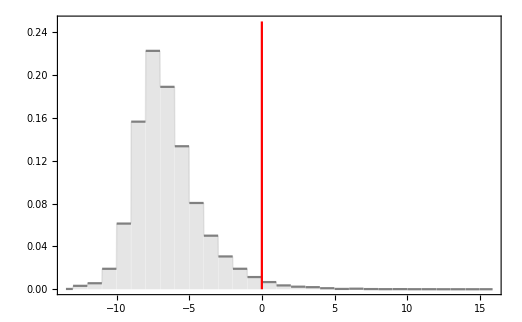

```mathematica
Show[plottest2,zeta1,Frame->True,PlotRange->All] (*Shows how much of the area under the curve satisfies zeta<1 from phase correction*)
```

```mathematica
Log[Max[ζphaseAll]]
```

15.8769

```mathematica
Log[Min[ζphaseAll]]
```

-13.4813

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]
```

0.999836

```mathematica
Integrate[ps2[x],{x,-Infinity,Infinity}]
```

1.

```mathematica
Integrate[ps2[x],{x,Log[Min[ζphaseAll]],0}]/Integrate[ps2[x],{x,Log[Min[ζphaseAll]],Log[Max[ζphaseAll]]}]*100 (*98% area under the curve satisfies zeta<1 from phase correction*)
```

98.2835

```mathematica
𝒟logamp=HistogramDistribution[Log[ζampAll]] (*zeta from log of amp correction from monte-carlo*)
```

DataDistribution[…]

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
Min[Log[ζampAll]]
```

-10.7176

```mathematica
Max[Log[ζampAll]]
```

19.4335

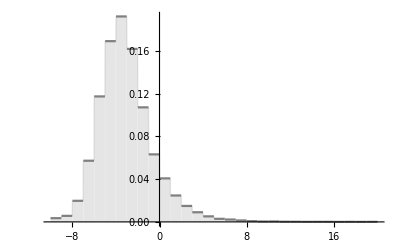

```mathematica
plottestamp=Plot[ps2amp[x],{x,-10,20},Filling->Axis,PlotStyle->Gray]
```

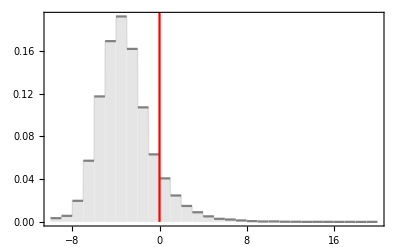

```mathematica
Show[plottestamp,zeta1,Frame->True]  (*Shows how much of the area under the curve satisfies zeta<1 from amplitude correction*)
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],0}]/Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]*100 (*89.7% area under the curve satisfies zeta<1 from amplitude correction*)
```

89.7039

```mathematica
Integrate[ps2amp[x],{x,Log[Min[ζampAll]],Log[Max[ζampAll]]}]
```

0.9998

```mathematica
fun2=PDF[𝒟log,Log[ζphaseAll]] (*pdf of log(sigma_zeta)|log_sigma_zeta*)
```

{0.222556,0.0500268,0.188969,0.133507,0.0500268,0.188969,0.222556,52238,0.222556,0.222556,0.0191189,0.188969,0.0500268,0.188969,0.188969}
 |  |  |  |

```mathematica
fun3=fun1*fun2
```

{168.406 ⅇ^(-1.79882×10^6 x^2),0.431147 ⅇ^(-233.343 x^2),50.5485 ⅇ^(-224795. x^2),52247,82.5992 ⅇ^(-600234. x^2),38.8896 ⅇ^(-133056. x^2)}
 |  |  |  |

```mathematica
(*Length[fun3]*)
```

```mathematica
(*fun4=fun3/.x->0.0000001*)
```

```mathematica
fun5=Transpose[{Log[ζphaseAll],fun3}]
```

{{-7.54789,168.406 ⅇ^(-1.79882×10^6 x^2)},{-3.07283,0.431147 ⅇ^(-233.343 x^2)},52249,{-6.24584,38.8896 ⅇ^(-133056. x^2)}}
 |  |  |  |

```mathematica
(*fun6=Interpolation[fun5]*)(*Unless we give a specific value of x, NIntegrate is not possible*)
```

```mathematica
(*NIntegrate[fun6[z],{z,0,1}]*)
```

```mathematica
ΔζphaseAll=Table[Abs[Log[ζphaseAll[[i+1]]]-Log[ζphaseAll[[i]]]],{i,1,Length[βppEAll]-1}] (* delta sigma_zeta *)
```

{4.47507,3.43522,1.15273,1.89889,3.37108,0.964872,1.56901,52237,0.0628702,0.236926,3.38505,3.73557,2.91202,3.1344,0.753273}
 |  |  |  |

```mathematica
fun7=Table[ΔζphaseAll[[i]]*fun3[[i]],{i,1,Length[ΔζphaseAll]}]
```

{753.629 ⅇ^(-1.79882×10^6 x^2),1.48108 ⅇ^(-233.343 x^2),58.2689 ⅇ^(-224795. x^2),52246,2.98325 ⅇ^(-1137.14 x^2),62.2197 ⅇ^(-600234. x^2)}
 |  |  |  |

```mathematica
fun8=Total[fun7] (*This is the pdf for zeta*)
```

1043.22 ⅇ^(-2.56248×10^11 x^2)+483.444 ⅇ^(-2.46016×10^11 x^2)+52247+4.83532×10^-11 ⅇ^(-8.85438×10^-15 x^2)+4.509×10^-11 ⅇ^(-8.09994×10^-15 x^2)
 |  |  |  |

```mathematica
(*fun8/.x->0.0000001*)
```

```mathematica
fun9[x_]=fun8
```

1043.22 ⅇ^(-2.56248×10^11 x^2)+483.444 ⅇ^(-2.46016×10^11 x^2)+52247+4.83532×10^-11 ⅇ^(-8.85438×10^-15 x^2)+4.509×10^-11 ⅇ^(-8.09994×10^-15 x^2)
 |  |  |  |

```mathematica
Sample= Table[10^-2*i,{i,-1000,1000}]//N;
```

```mathematica
points=Table[Sample[[i]],{i,1,2001}];(*These are the values of zeta that we are going to use for plotting the pdf of zeta. I am considering from -10 to 10 as suggested by you. But we don't know any good reason behind this except the fact that it is going to take more time if you go beyond this. Technincally, we are supposed to find the pdf upto 300, since it is mean of zeta from monte-carlo*)
```

```mathematica
pdfzeta=Map[fun9,ζSampleLog] (*This is going to take about five minutes.*)
```

General::munfl: Exp[-1020.14] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-979.408] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-976.214] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{1.53605×10^7,1.47753×10^7,1.46428×10^7,1.44856×10^7,1.42939×10^7,1.4053×10^7,1.37463×10^7,1.33598×10^7,1.28826×10^7,1.23035×10^7,1.1612×10^7,1.08083×10^7,9.90733×10^6,8.92534×10^6,7.87007×10^6,6.75882×10^6,5.64084×10^6,4.58293×10^6,3.63212×10^6,2.80511×10^6,2.10731×10^6,1.5431×10^6,1.10903×10^6,788246.,556775.,391064.,272123.,187176.,127641.,86601.6,58311.7,38815.2,25721.3,17208.1,11660.1,7909.78,5329.25,3578.08,2402.29,1604.42,1062.,703.405,470.145,314.818,208.795,137.238,90.1713,59.3398,38.7313,24.9069,15.8973,10.1936,6.55718,4.19161,2.6787,1.72568,1.109,0.703023,0.445564,0.28954,0.194079,0.132748,0.0919859,0.0642112,0.0449498,0.0313783,0.0215411,0.0143952,0.00931553,0.00578674,0.0034327,0.00197869}

```mathematica
pdfzeta2=Transpose[{ζSampleLog,pdfzeta}];
```

```mathematica
fun10=Interpolation[pdfzeta2,InterpolationOrder->1];
```

```mathematica
AreaPDF=(NIntegrate[fun10[z],{z,Min[ζSampleLog],Max[ζSampleLog]}]) (*To normalize the pdf*)
```

7655.8

```mathematica
pdfζphaseNormalized=Transpose[{ζSampleLog,pdfzeta/AreaPDF}];
```

```mathematica
pdfζphaseNormalized2=Interpolation[pdfζphaseNormalized];
```

```mathematica
cdfζphaseNormalized=Table[{ζSampleLog[[i]],NIntegrate[pdfζphaseNormalized2[x],{x,0,ζSampleLog[[i]]}]},{i,1,Length[ζSampleLog]}];
```

```mathematica
cdfζphaseNormalized2=Interpolation[cdfζphaseNormalized,x];
```

```mathematica
cdfζphaseNormalized3[x_]=cdfζphaseNormalized2
```

InterpolatingFunction[…][x]

## More accurate Integration for ζ

### 2D Gaussian, ζ samples

```mathematica
fun1Kent[x_,y_]=1/(√(2*π) Exp[y])*Exp[-x^2/(2Exp[2y])];
```

ζ sample

```mathematica
ζSampleLog=Prepend[10^Range[-5,2,0.1],0]
```

{0,0.00001,0.0000125893,0.0000158489,0.0000199526,0.0000251189,0.0000316228,0.0000398107,0.0000501187,0.0000630957,0.0000794328,0.0001,0.000125893,0.000158489,0.000199526,0.000251189,0.000316228,0.000398107,0.000501187,0.000630957,0.000794328,0.001,0.00125893,0.00158489,0.00199526,0.00251189,0.00316228,0.00398107,0.00501187,0.00630957,0.00794328,0.01,0.0125893,0.0158489,0.0199526,0.0251189,0.0316228,0.0398107,0.0501187,0.0630957,0.0794328,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.}

Creating a table for fun1Kent[x,y] at each ζ sample for x

```mathematica
fun1TableLog[y_]=Table[{ζSampleLog[[i]],fun1Kent[ζSampleLog[[i]],y]},{i,1,Length[ζSampleLog]}];
```

### Creating an interpolation function for the Monte-Carlo probability distribution on σ_Σ

```mathematica
ζMC[x_]=ps1;
```

```mathematica
ζMC[-14.5]
ζMC[16.5]
```

0.

0.

ζ sample for creating an interpolation function for the MC prob distribution
Since ζ > 0, I only consider positive ζ

```mathematica
ζMCSample=Range[-14.5,16.5,1];
```

creating a table for the MC distribution at each sample ζ

```mathematica
ζMCTable=Table[{ζMCSample[[i]],ζMC[ζMCSample[[i]]]},{i,1,Length[ζMCSample]}];
```

creating an interpolation function

```mathematica
ζMCTableInterp=Interpolation[ζMCTable];
```

Plot

```mathematica
plotζMCTableInterp=Plot[ζMCTableInterp[x],{x,-14.5,16.5},PlotStyle->Blue,PlotLegends->{"Interpolation"}];
```

Comparison with the actual distribution

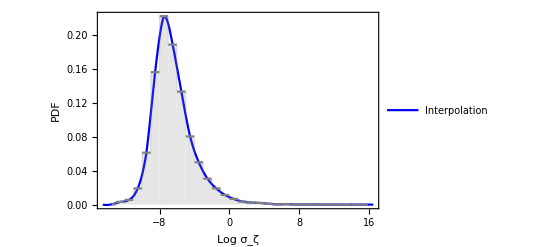

```mathematica
Show[plotζMCTableInterp,plottest2,Frame->True,FrameLabel->{"Log σ_ζ","PDF"}]
```

Nice agreement!

### Finding PDF for ζ

```mathematica
MaxLogζphase=Log[Max[ζphaseAll]]
MinLogζphase=Log[Min[ζphaseAll]]
```

15.8769

-13.4813

#### Raw Distribution

Creating a table for ∫ P(ζ|σ_Σ) P(σ_Σ) dσ_Σ for each sample ζ using NIntegrate

```mathematica
ζFinalPDFPhaseLog=Table[{fun1TableLog[y][[i,1]],NIntegrate[fun1TableLog[y][[i,2]]ζMCTableInterp[y],{y,MinLogζphase,MaxLogζphase}]},{i,1,Length[fun1TableLog[y]]}];
```

Comparison with Sharaban’s result (there’s a big difference between the two)

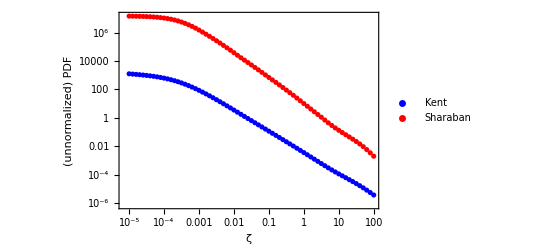

```mathematica
ListLogLogPlot[{ζFinalPDFPhaseLog,pdfzeta2},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"Kent","Sharaban"},FrameLabel->{"ζ","(unnormalized) PDF"}]
```

#### Normalized Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLog=Interpolation[ζFinalPDFPhaseLog];
```

Normalization

```mathematica
Normalization=NIntegrate[ζFinalPDFPhaseInterpLog[x],{x,0,100}]
```

0.498499

Normalized distribution

```mathematica
ζFinalPDFPhaseLogNorm=Table[{ζFinalPDFPhaseLog[[i,1]],ζFinalPDFPhaseLog[[i,2]]/Normalization},{i,1,Length[ζFinalPDFPhaseLog]}];
```

Plot

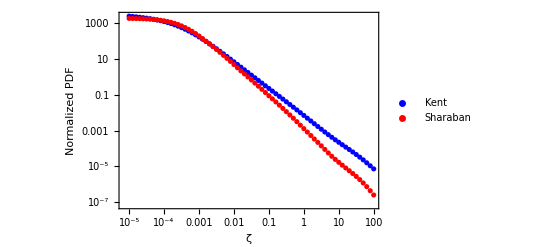

```mathematica
ListLogLogPlot[{ζFinalPDFPhaseLogNorm,pdfζphaseNormalized},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"Kent","Sharaban"},FrameLabel->{"ζ","Normalized PDF"}]
```

#### Cumulative Distribution

Interpolation

```mathematica
ζFinalPDFPhaseInterpLogNorm=Interpolation[ζFinalPDFPhaseLogNorm];
```

Creating a table for cumulative distribution

```mathematica
ζFinalCDFPhaseNorm=Table[{ζSampleLog[[i]],NIntegrate[ζFinalPDFPhaseInterpLogNorm[x],{x,0,ζSampleLog[[i]]}]},{i,1,Length[ζSampleLog]}];
```

#### Finding 90% credible limit for ζ

Interpolation for CDF

```mathematica
ζFinalCDFPhaseNormInterp=Interpolation[ζFinalCDFPhaseNorm];
```

90% limit

```mathematica
FindRoot[ζFinalCDFPhaseNormInterp[x]==0.9,{x,0.02}]
```

{x→0.0201651}

```mathematica
FindRoot[cdfζphaseNormalized3[x]==0.9,{x,0.01}] (*Differs from yours by 50%*)
```

{x→0.0067638}

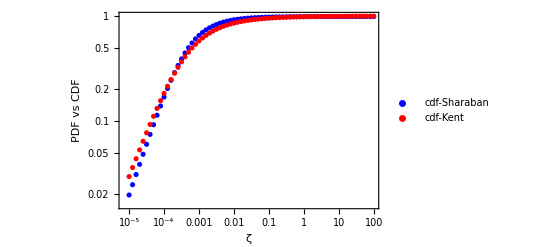

```mathematica
ListLogLogPlot[{cdfζphaseNormalized,ζFinalCDFPhaseNormInterp},PlotRange->All,Frame->True,PlotStyle->{Blue,Red},PlotLegends->{"cdf-Sharaban","cdf-Kent"},FrameLabel->{"ζ","PDF vs CDF"}]
```